```mathematica
lst1= List[];
lst1=Import["C:/Users/Артем/Desktop/соду.txt","Table"];
lst4= List[];
lst4=Import["C:/Users/Артем/Desktop/соду2.txt","Table"];
lst2= List[];
lst2=Import["C:/Users/Артем/Desktop/ур1.txt","Table"];
lst3= List[];
lst3=Import["C:/Users/Артем/Desktop/ур2.txt","Table"];
lst5= List[];
lst5=Import["C:/Users/Артем/Desktop/сур1.txt","Table"];
lst6= List[];
lst6=Import["C:/Users/Артем/Desktop/сур2.txt","Table"];
```

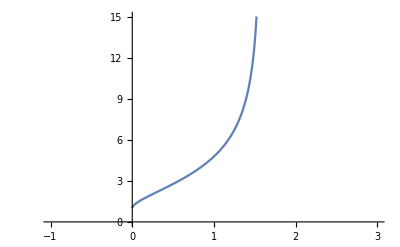

```mathematica
Plot[E^(Sqrt[2*Log[Tan[x/2+Pi/4]]]),{x,-1,3}]
```

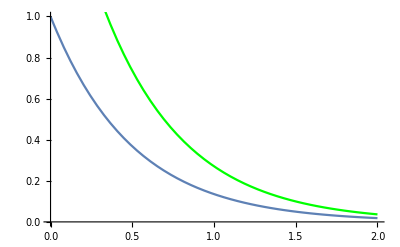

```mathematica
Show[Plot[E^(-2x),{x,0,2}],Plot[2E^(-2x),{x,0,2},PlotStyle->Green]]
```

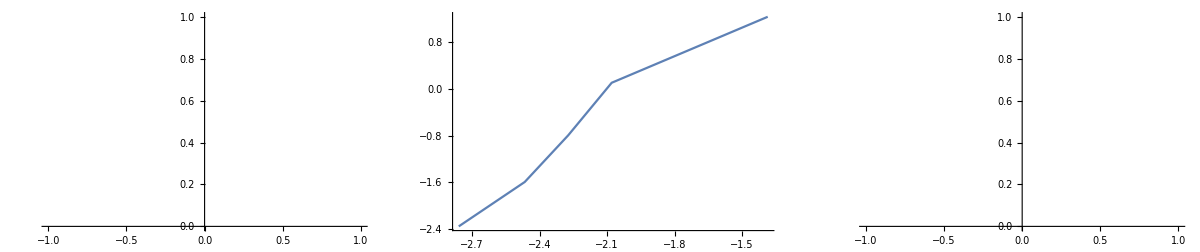

```mathematica
GraphicsRow[{ListLinePlot[lst4, PlotStyle->Green,PlotRange->Full],ListLinePlot[lst1,PlotRange->Full],Show[ListLinePlot[lst4, PlotStyle->Green,PlotRange->Full],ListLinePlot[lst1,PlotRange->Full]]}]
```

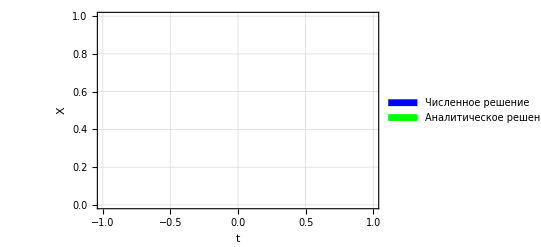

```mathematica
Show[ListLinePlot[lst4, PlotStyle->Green,PlotRange->Full ,GridLines->Automatic, Frame->True, FrameLabel->{Style[t, Black, Medium],Style[X, Black, Medium]}, RotateLabel->False],ListLinePlot[lst1,PlotRange->Full, GridLines->True ,PlotMarkers->{Automatic, 3}, PlotStyle->{Thickness[0.002]},PlotLegends->Placed[SwatchLegend[{Blue,Green},{"Численное решение","Аналитическое решение"}], {0.85,0.10}]]]
```

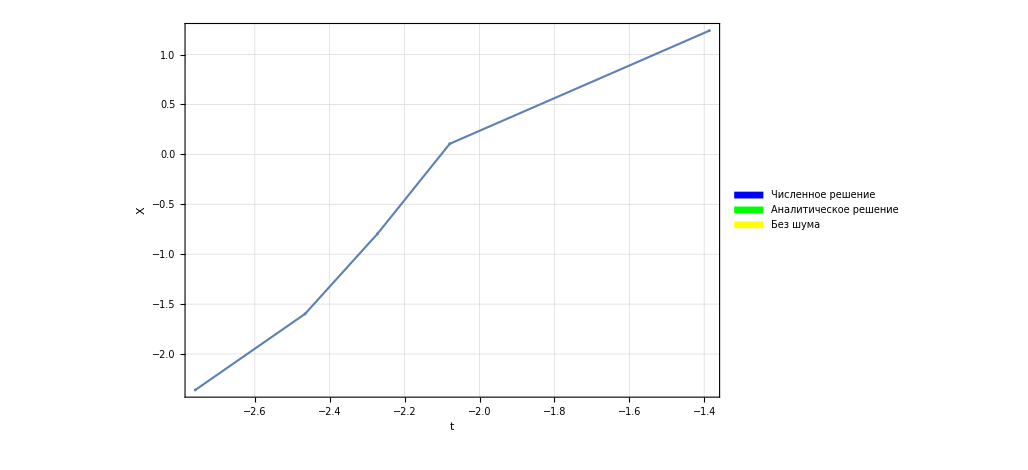

```mathematica
Show[ListLinePlot[lst1,PlotRange->Full, GridLines->Automatic ,Frame->True, FrameLabel->{Style[t, Black, Medium],Style[X, Black, Medium]}, RotateLabel->False,PlotMarkers->{Automatic, 3}, PlotStyle->{Thickness[0.002]},PlotLegends->Placed[SwatchLegend[{Blue,Green, Yellow},{"Численное решение","Аналитическое решение", "Без шума"}], {0.85,0.10}]],ListLinePlot[lst4, PlotStyle->Green,PlotRange->Full ,GridLines->Automatic ], Plot[(1.5*(E^(2x))-0.5)/(1.5*(E^(2x))+0.5),{x,0,2}, PlotStyle->Yellow,GridLines->Automatic]]
```

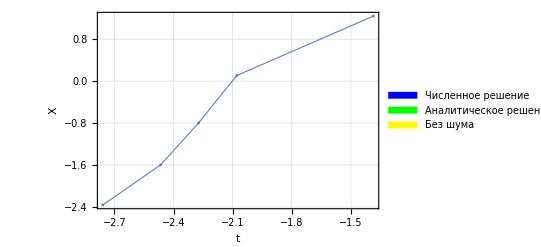

```mathematica
Show[ListLinePlot[lst1,PlotRange->Full, GridLines->Automatic ,Frame->True, FrameLabel->{Style[t, Black, Medium],Style[X, Black, Medium]}, RotateLabel->False,PlotMarkers->{Automatic, 3}, PlotStyle->{Thickness[0.002]},PlotLegends->Placed[SwatchLegend[{Blue,Green, Yellow},{"Численное решение","Аналитическое решение", "Без шума"}], {0.85,0.10}]],ListLinePlot[lst4, PlotStyle->Green,PlotRange->Full ,GridLines->Automatic ], Plot[1.5*(E^((2-1/2)x)),{x,0,2}, PlotStyle->Yellow,GridLines->Automatic]]
```

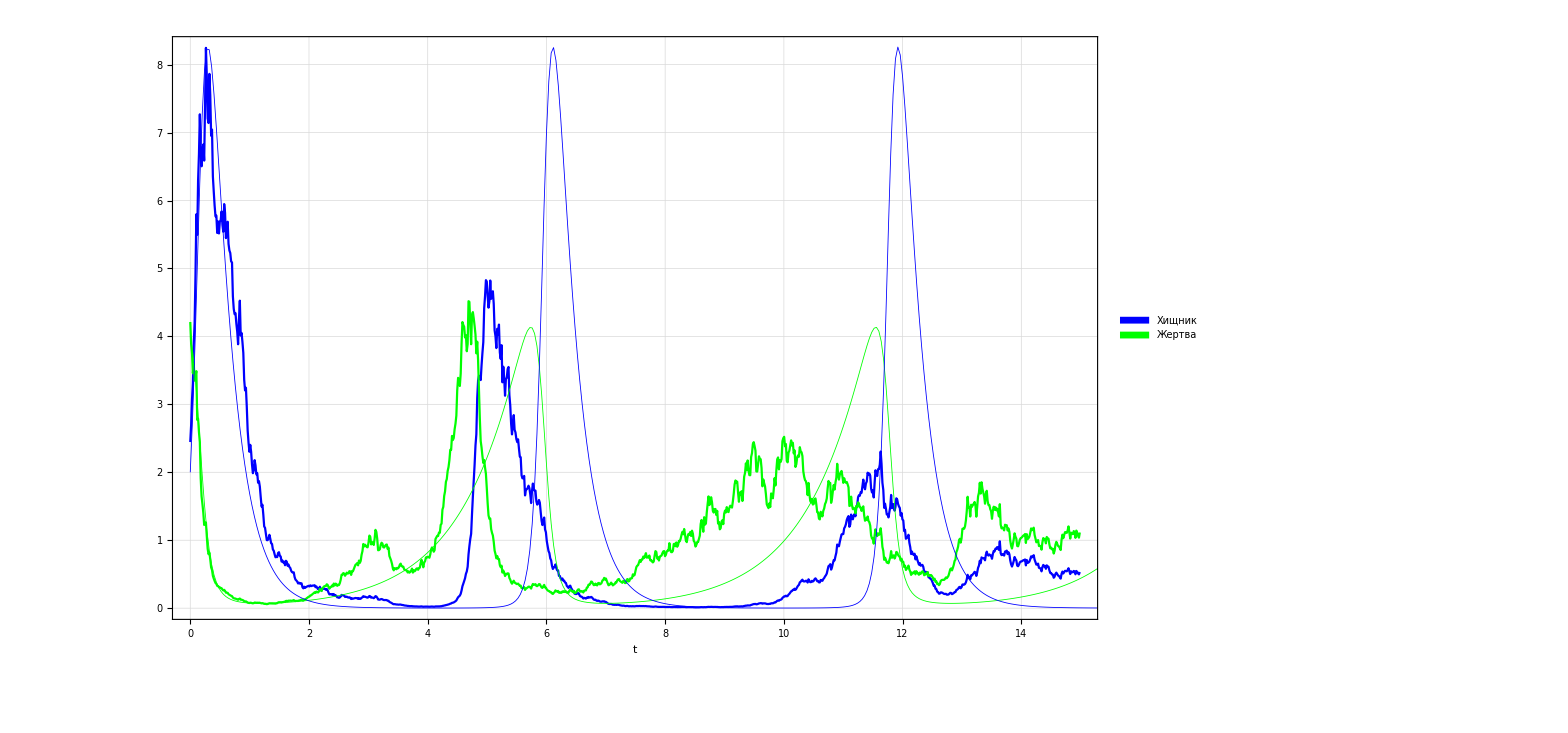

```mathematica
Show[ListLinePlot[lst6, PlotStyle->Blue,GridLines->Automatic, PlotRange->Full,Frame->True,FrameLabel->{Style[t, Black, Medium]}, PlotLegends->Placed[SwatchLegend[{Blue,Green},{"Хищник","Жертва"}], {0.93,0.85}]],ListLinePlot[lst5, PlotStyle->Green,PlotRange->Full],ListLinePlot[lst2,PlotStyle->{Green,Thickness[0.0005]},PlotRange->{{0,15},{0,10}}],ListLinePlot[lst3,PlotStyle->{Blue,Thickness[0.0005]}, PlotRange->{{0,15},{0,10}}]]
```

```mathematica
{xslv, yslv} = DSolve[{x'[t] == x[t]-1*x[t]*y[t], y'[t] == 3x[t]*y[t]-1/3*y[t]},{x,y}, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::shape: Lists {xslv,yslv} and {{y→Function[{t},-ProductLog[-Power[«2»] Power[«2»]]],x→Function[{t},InverseFunction[Integrate[Times[«2»],{«3»}]&][t+2]]}} are not the same shape.

{{y→Function[{t},-ProductLog[-(ⅇ^(-C[1]+3 InverseFunction[1/(K[1] (1+ProductLog[-ⅇ^(-C[1]+3 K[1])/K[1]^(1/3)]))K[1]1#1&][t+C[2]]))/((InverseFunction[1/(K[1] (1+ProductLog[-ⅇ^(-C[1]+3 K[1])/K[1]^(1/3)]))K[1]1#1&][t+C[2]])^(1/3))]],x→Function[{t},InverseFunction[1/(K[1] (1+ProductLog[-ⅇ^(-C[1]+3 K[1])/K[1]^(1/3)]))K[1]1#1&][t+C[2]]]}}

```mathematica
Simplify[DSolve[{y'[x]==y[x]-1*y[x]*z[x],z'[x]==3y[x]*z[x]-1/3*z[x],y[0]==1},{y,z},x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
DSolve[{y'[x]==Exp[z[x]]+1,z'[x]==y[x]-x,y[0]==0},{y,z},x]//Quiet
```

{{z→Function[{x},-∞],y→Function[{x},x]},{z→Function[{x},Log[C[1]+C[1] Tan[(x √C[1])/(√2)]^2]],y→Function[{x},x+√2 √C[1] Tan[(x √C[1])/(√2)]]}}

```mathematica
params={α->1,γ->3,β->1,δ->3,Subscript[r, 0]->4,Subscript[f, 0]->2,R->40};
sol=NDSolve[{r'[t]==α r[t]-β f[t]r[t]+с,f'[t]==-γ f[t]+δ f[t]r[t],r[0]==Subscript[r, 0],f[0]==Subscript[f, 0]}/.params,{r[t],f[t]},{t,0,10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{r'[t]==с+r[t]-f[t] r[t],f'[t]==-3 f[t]+3 f[t] r[t],r[0]==4,f[0]==2},{r[t],f[t]},{t,0,10}]

```mathematica
Plot[{f[t]/.sol,r[t]/.sol},{t,0,10}, PlotRange->All,AxesLabel->{"t","f(t),r(t)"}]
```

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{r'[0.000204286]==с+r[0.000204286]-f[0.000204286] r[0.000204286],f'[0.000204286]==-3 f[0.000204286]+3 f[0.000204286] r[0.000204286],r[0]==4,f[0]==2},{r[0.000204286],f[0.000204286]},{0.000204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{r'[0.000204286]==с+r[0.000204286]-1. f[0.000204286] r[0.000204286],f'[0.000204286]==-3. f[0.000204286]+3. f[0.000204286] r[0.000204286],r[0.]==4.,f[0.]==2.},{r[0.000204286],f[0.000204286]},{0.000204286,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{r'[0.204286]==с+r[0.204286]-f[0.204286] r[0.204286],f'[0.204286]==-3 f[0.204286]+3 f[0.204286] r[0.204286],r[0]==4,f[0]==2},{r[0.204286],f[0.204286]},{0.204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

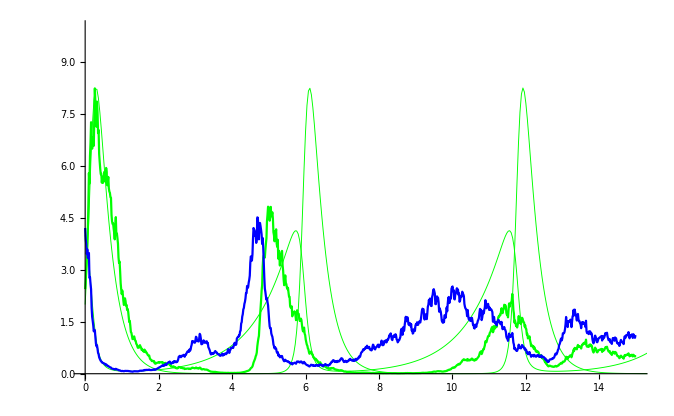

```mathematica
Show[ListLinePlot[lst2,PlotStyle->{Green,Thickness[0.001]},PlotRange->{{0,15},{0,10}}],ListLinePlot[lst3,PlotStyle->{Green,Thickness[0.001]}, PlotRange->{{0,15},{0,10}}],ListLinePlot[lst6,PlotStyle->Green ,PlotRange->{{0,15},{0,10}}],ListLinePlot[lst5,PlotStyle->Blue ,PlotRange->{{0,15},{0,10}}]]
```

```mathematica
DSolve[y''''[x]+4y''[x]+4y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[√2 x]+x C[2] Cos[√2 x]+C[3] Sin[√2 x]+x C[4] Sin[√2 x]}}

```mathematica
DSolve[y'[x]+y[x]*Cos[x]==E^-Sin[x], y[0]==0, y[x]]
```

DSolve::dsfun: y[0]==0 cannot be used as a function.

DSolve[Cos[x] y[x]+y'[x]==ⅇ^(-Sin[x]),y[0]==0,y[x]]

```mathematica
DSolve[{y'[x]==x^2+x,y[0]==2},y,x]
```

{{y→Function[{x},1/6 (12+3 x^2+2 x^3)]}}

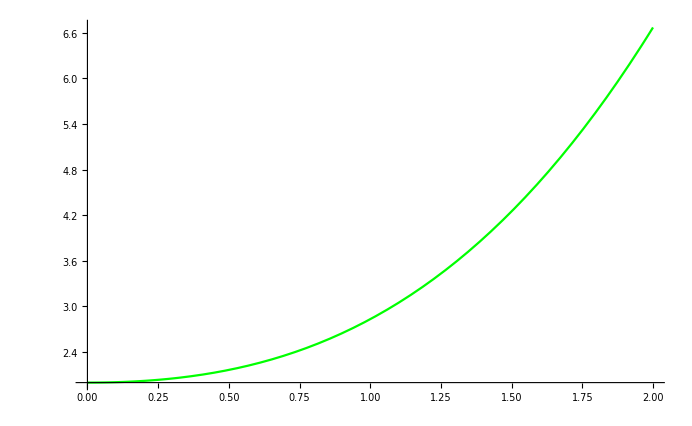

```mathematica
Show[Plot[1/6 (12+3 x^2+2 x^3) ,{x,0,2},PlotStyle->Green],ListLinePlot[lst1]]
```

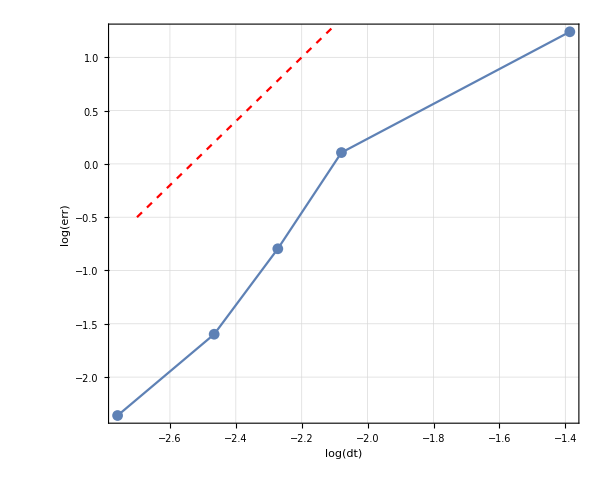

```mathematica
Show[ListPlot[lst1,GridLines->Automatic,AspectRatio->1/1.2,Frame->True,FrameLabel->{Style["log(dt)", Black, Medium],Style["log(err)", Black, Medium]}, RotateLabel->False],ListLinePlot[lst1,Frame->True],Plot[3x+7.6,{x,-2.7,-2.1},PlotStyle->{Dashed, Red},Frame->True] ]
```